### Basic Examples

```mathematica
associativity=DiagramComposition[Diagram[f_,{p_,p3_},p4_],Diagram[f_,{p1_,p2_},p_]]->DiagramComposition[Diagram[f,{p1,p},p4],Diagram[f,{p2,p3},p]]
```

-Graphics-→-Graphics-

```mathematica
coassociativity=
DiagramComposition[Diagram[f_,p_,{p2_,p3_}],Diagram[f_,p1_,{p_,p4_}]]->DiagramComposition[Diagram[f,p,{p3,p4}],Diagram[f,p1,{p2,p}]]
```

-Graphics-→-Graphics-

```mathematica
diag=Diagram[DiagramRightComposition[DiagramProduct[Diagram[C,p],DiagramComposition[Diagram[B,p,{p,p}],Diagram[B,p,{p,p}]]],DiagramComposition[Diagram[A,{p,p},p],DiagramProduct[Diagram[A,{p,p},p],IdentityDiagram[p]]],Diagram[D,p,p]]]
```

-Graphics-

```mathematica
DiagramReplaceList[diag,associativity]
```

{-Graphics-}

```mathematica
DiagramReplaceList[diag,{associativity,coassociativity}]
```

{-Graphics-}

### Lambdas

```mathematica
<<Wolfram`Lambda`
```

#### Remove

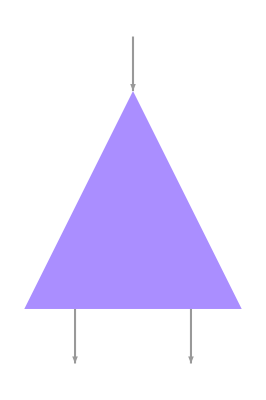
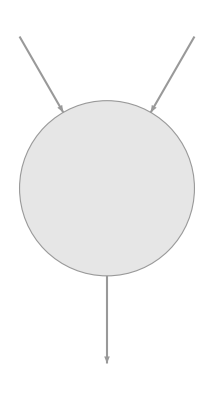
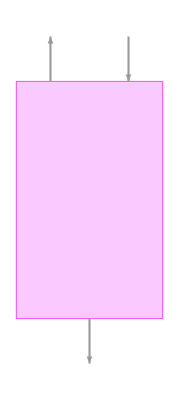

```mathematica
{copy,app,lambda}=DiagramSubdiagrams[SimplifyDiagram@ToDiagramNetwork@LambdaStringDiagram[λ[1[1]]],{1}]
```

```mathematica
lambda=DiagramExpressionReplace[lambda,Subscript["λ",_]->Subscript["λ",x_]]
```

-Graphics-

```mathematica
sourceDiagram=DiagramExpressionReplace[LambdaStringDiagram[λ[1[1]],"LambdaSize"->.15,Dividers->All],Subscript["λ",_]->Subscript["λ",x_]]
```

-Graphics-

```mathematica
targetDiagram=LambdaStringDiagram[TagLambda[λ[1],{x}],"LambdaSize"->.15,Dividers->All]
```

-Graphics-

```mathematica
DiagramReplaceList[sourceDiagram,RemoveDiagramRule[lambda]]
```

{-Graphics-}

```mathematica
diagram=LambdaStringDiagram[λ[λ[1[1]][1[1][λ[2[1[1]]]]]],"LambdaSize"->.15,Dividers->True]
```

-Graphics-

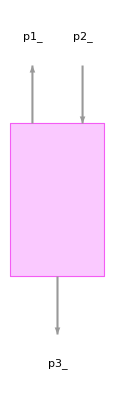
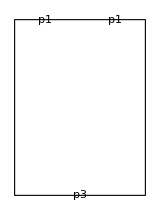
-Graphics-→-Graphics-

```mathematica
RemoveDiagramRule[lambda]
```

```mathematica
DiagramReplaceList[diagram,RemoveDiagramRule[lambda]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
subDiagram=DiagramExpressionReplace[LambdaStringDiagram[λ[2[1[1]]],"LambdaSize"->.15,Dividers->All],Subscript["λ",_]->Subscript["λ",x_]]
```

-Graphics-

```mathematica
DiagramReplaceList[diagram,RemoveDiagramRule[subDiagram]]
```

{-Graphics-}

```mathematica
DiagramReplaceList[-Graphics-,{RemoveDiagramRule[copy],RemoveDiagramRule[lambda]}]
```

{-Graphics-,-Graphics-}

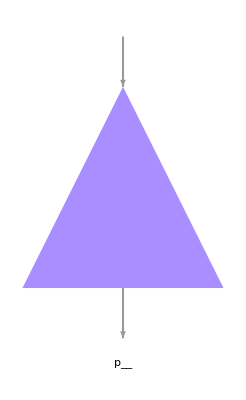

```mathematica
multiCopy=Diagram[copy,Inherited,p,"PortLabels"->{Inherited,p__}]
```

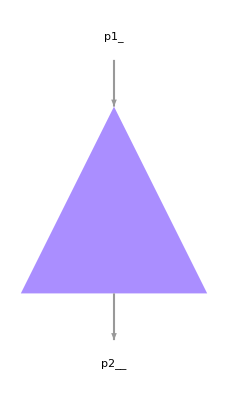
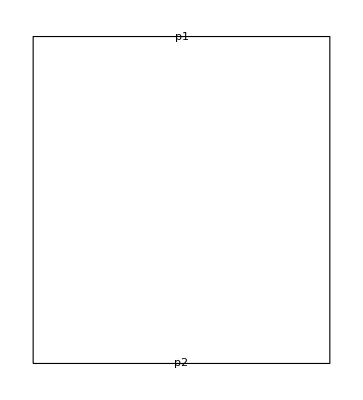
-Graphics-→-Graphics-

```mathematica
revemoMultiCopy=MapAt[Diagram[#,"PortLabels"->{Inherited,p2__}]&,{1}]@RemoveDiagramRule[Diagram[copy,Inherited,p]]
```

```mathematica
DiagramReplaceList[diagram,revemoMultiCopy]
```

{-Graphics-,-Graphics-,-Graphics-}

#### BetaReduce

```mathematica
term=LambdaStringDiagram[λ[1[1]][λ[1]],"LambdaSize"->.15,Dividers->True,"Rotate"->False]
```

-Graphics-

```mathematica
betaReduce=DiagramComposition[Diagram[app,{arg_,λ_},beta_,"PortLabels"->Automatic],Diagram[lambda,{SuperStar[var_],body_},{λ_},"PortLabels"->Automatic],Alignment->Center]->DiagramProduct[IdentityDiagram[body->beta],IdentityDiagram[var->arg]]
```

-Graphics-→-Graphics-

```mathematica
LambdaStringDiagram[λ[λ[1]],"AddErasers"->True]
```

-Graphics-

```mathematica
dupReduce=DuplicateRule[{SuperStar[x1],x2},{out1,out2}]
```

-Graphics-→-Graphics-

```mathematica
dupDupReduce=DuplicateAnnihilateRule[{SuperStar[in1],SuperStar[in2]},{out1,out2},"Bend"->True]
```

-Graphics-→-Graphics-

```mathematica
DiagramReplace[LambdaStringDiagram[λ[λ[1[1]]][λ[1]],"LambdaSize"->0.15,"AddErasers"->True,"Rotate"->False],betaReduce]
```

-Graphics-

#### Lambda interaction networks

```mathematica
LambdaInteractionNet[λ[1[1]]]
```

-Graphics-

```mathematica
betaReduce=AnnihilateRule[Subscript["λ", _],"\[Application]",{var,SuperStar[body]},{SuperStar[arg],beta},"Shape"->"Triangle","ShowLabel"->False]
```

-Graphics-→-Graphics-

```mathematica
dupReduce=DuplicateRule[{x1,SuperStar[x2]},{out1,out2}]
```

-Graphics-→-Graphics-

```mathematica
dupDupReduce=DuplicateAnnihilateRule[{SuperStar[in1],SuperStar[in2]},{out1,out2}]
```

-Graphics-→-Graphics-

```mathematica
LambdaStringDiagram[λ[1][λ[1]]]
DiagramReplaceList[%,betaReduce,"Return"->"Rule"]
```

-Graphics-

-Graphics-

```mathematica
LambdaStringDiagram[TagLambda[#],"LambdaSize"->.15]&/@BetaReduceList[TagLambda@λ[1[1]][λ[1]],2]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
LambdaStringDiagram[λ[λ[1[1]]],"AddErasers"->True]
```

-Graphics-

```mathematica
DuplicateRule[{x1,SuperStar[x2]},{out1,SuperStar[out2]}]
```

-Graphics-→-Graphics-

```mathematica
DiagramReplaceList[{betaReduce(*,dupDupReduce,dupReduce*)}]@LambdaStringDiagram[λ[λ[1[2]]][λ[1]],"LambdaSize"->.15]
```

{{-Graphics-}}

```mathematica
CanonicalHypergraph[#,"Annotations"->True]&/@{DiagramHypergraph@-Graphics-,DiagramHypergraph@-Graphics-}
SameQ@@%
```

{-Graphics-,-Graphics-}

True

```mathematica
Row@NestList[DiagramReplace[$LambdaInteractionRules],LambdaInteractionNet[λ[λ[2[1]]][λ[1]],"LambdaSize"->.15,"AddErasers"->True],3]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
LambdaInteractionNet[FunctionLambda[λ[n,λ[f,λ[x,f[n[f][x]]]]]]@ChurchNumeral[0],"Arrange"->False]
NestList[DiagramReplace[$LambdaInteractionRules],%,4]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LambdaInteractionNet[TagLambda[#,"Simple"],"LambdaSize"->.15]&/@BetaReduceList[TagLambda@λ[λ[1[2]]][λ[1]],2]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Row@NestList[DiagramReplace[{betaReduce,dupDupReduce,dupReduce}],LambdaStringDiagram[λ[λ[1[1]]],"LambdaSize"->.15],1]
```

```mathematica
copyFlip=DiagramReverse@DiagramArrange[DiagramNetwork@CopyDiagram[x_,{y_,x_},"Shape"->"Triangle","Width"->1],"Rotate"->True]->DiagramArrange@DiagramNetwork@CopyDiagram[SuperStar[y],{x,SuperStar[x]},"Shape"->"Triangle","Width"->1]
```

-Graphics-→-Graphics-

```mathematica
With[{init=ToDiagramNetwork@LambdaInteractionNet[λ[1[λ[1[2]]]][λ[1]]]},
Block[{visited=<|CanonicalHypergraph[DiagramHypergraph[init](*,"Annotations"->True*)]->init|>},
Nest[
With[{results=Catenate@Map[Catenate@*DiagramReplaceList[{betaReduce,dupDupReduce,dupReduce}],#]},
With[{hg=CanonicalHypergraph[DiagramHypergraph[#](*,"Annotations"->True*)]},If[KeyExistsQ[visited,hg],Nothing,AppendTo[visited,hg->#];#]]&/@results
]&,
{init},
5
];
Values@visited
]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FixedPointList[DiagramReplace[{betaReduce,dupDupReduce,dupReduce}],LambdaInteractionNet[λ[1[1]][λ[1]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FixedPointList[DiagramReplace[{betaReduce,dupDupReduce,dupReduce}],LambdaInteractionNet[λ[1[1]][λ[1]],"Arrange"->False]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FixedPointList[DiagramReplace[{betaReduce,dupDupReduce,dupReduce,EraserRule[{SuperStar[in1],in2}],AnnihilateRule[None,None,{},{},"Shape"->"Triangle","FloatingPorts"->True]}],LambdaInteractionNet[λ[λ[1[1]]][λ[1]],"Arrange"->True]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Molecule

```mathematica
dielsAlder=PatternReaction["[C:1]=[C:2][C:3]=[C:4].[C:5]=[C:6]>>[C:1]1[C:2]=[C:3][C:4][C:5][C:6]1"]
```

-Graphics-

```mathematica
dielsAlder["Reactants"]
```

{MoleculePattern[…],MoleculePattern[…]}

```mathematica
dielsAlder["Products"]
```

{MoleculePattern[…]}

```mathematica
AtomCount@dielsAlder["Reactants"][[1]]
```

4

```mathematica
-Graphics-@-Graphics-
```

{<|Hypergraph→-Graphics-,MatchVertices→{1,2,3,4,5,6},MatchEdges→{{1,2},{2,3},{4,6},{5,6}},MatchEdgePositions→{{1},{2},{3},{4}},NewVertices→{},NewEdges→{{1,2},{4,6},{5,6},{3,6}},DeletedVertices→{},RuleVertexMap→{1:>1,2:>2,3:>3,4:>4,5:>5,6:>6},Bindings→<|v2408743496341336592_:>1,v8279773449723746393_:>2,v5316481726667883800_:>3,v8749396470226027473_:>4,v9144142082290548317_:>6,v6682695405924005767_:>5|>|>,<|Hypergraph→-Graphics-,MatchVertices→{1,2,3,4,5,6},MatchEdges→{{1,2},{2,3},{5,6},{4,6}},MatchEdgePositions→{{1},{2},{4},{3}},NewVertices→{},NewEdges→{{1,2},{5,6},{4,6},{3,6}},DeletedVertices→{},RuleVertexMap→{1:>1,2:>2,3:>3,4:>5,5:>4,6:>6},Bindings→<|v2408743496341336592_:>1,v8279773449723746393_:>2,v5316481726667883800_:>3,v8749396470226027473_:>5,v9144142082290548317_:>6,v6682695405924005767_:>4|>|>}